```mathematica
Quit
```

```mathematica
variableNames={"basis"};

Do[Module[{expr,file,txt},expr=ToExpression[name];
file=FileNameJoin[{NotebookDirectory[],"storage",name<>"_three-site"}];
(*Get the string with the actual ⟨ ⟩ glyphs,then replace them*)txt=ToString[expr,StandardForm];
txt=StringReplace[txt,{"⟨"->"\\[LeftAngleBracket]","⟩"->"\\[RightAngleBracket]"}];
Export[file,name<>" = "<>txt<>";\n","Text","CharacterEncoding"->"ASCII"];],{name,variableNames}];
```

# INTSECA

This notebook contains details of using twisted intersection theory to generate the master integrals and the associated canonical system for the three-site chain.

```mathematica
SetDirectory[NotebookDirectory[]];
<<INTSECA.wl
```

INTSECA 1.2.0

Union::normal: Nonatomic expression expected at position 1 in Union[Global`powers].

## 3-site chain

### Definitions

```mathematica
dim=3;
nkin=5;
kin={X1,X2,X3,Y12,Y23};
```

Untwisted hyperplanes:

```mathematica
nBplane=6;
B[1]={1,0,0,X1+Y12}; 
B[2]={0,1,0,X2+Y12+Y23};
B[3]={0,0,1,X3+Y23};
B[4]={1,1,1,X1+X2+X3};
B[5]={1,1,0,X1+X2+Y23}; 
B[6]={0,1,1,X2+X3+Y12};
```

Twisted hyperplanes:

```mathematica
nTplane=3;
T[1]={1,0,0,0};
T[2]={0,1,0,0};
T[3]={0,0,1,0};
powers={e,e,e};
```

Wavefunction:

```mathematica
psi=⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

51

```mathematica
sol=Sol[]
```

{⟨1,2,9⟩→0,⟨1,3,8⟩→0,⟨1,4,9⟩→-⟨1,4,8⟩,⟨1,5,9⟩→0,⟨1,6,9⟩→-⟨1,6,8⟩,⟨1,8,9⟩→0,⟨2,3,7⟩→0,⟨2,4,9⟩→-⟨2,4,7⟩,⟨2,5,9⟩→0,⟨2,6,7⟩→0,⟨2,7,9⟩→0,⟨3,4,8⟩→-⟨3,4,7⟩,⟨3,5,8⟩→-⟨3,5,7⟩,⟨3,6,7⟩→0,⟨3,7,8⟩→0,⟨4,5,6⟩→-⟨2,4,5⟩-⟨2,4,6⟩-⟨2,5,6⟩,⟨4,5,8⟩→-⟨4,5,7⟩,⟨4,6,9⟩→-⟨4,6,8⟩,⟨4,7,9⟩→-⟨4,7,8⟩,⟨4,8,9⟩→⟨4,7,8⟩,⟨5,6,9⟩→-⟨5,6,7⟩-⟨5,6,8⟩,⟨5,7,9⟩→0,⟨5,8,9⟩→0,⟨6,7,8⟩→0,⟨6,7,9⟩→0,⟨7,8,9⟩→0}

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({4} | {⟨4,7,8⟩}
{1,4} | {⟨1,4,8⟩}
{1,6} | {⟨1,6,8⟩}
{2,4} | {⟨2,4,7⟩}
{3,4} | {⟨3,4,7⟩}
{3,5} | {⟨3,5,7⟩}
{4,5} | {⟨4,5,7⟩}
{4,6} | {⟨4,6,8⟩}
{5,6} | {⟨5,6,7⟩,⟨5,6,8⟩}
{1,2,3} | {⟨1,2,3⟩}
{1,2,4} | {⟨1,2,4⟩}
{1,2,6} | {⟨1,2,6⟩}
{1,3,4} | {⟨1,3,4⟩}
{1,3,5} | {⟨1,3,5⟩}
{1,3,6} | {⟨1,3,6⟩}
{1,4,5} | {⟨1,4,5⟩}
{1,5,6} | {⟨1,5,6⟩}
{2,3,4} | {⟨2,3,4⟩}
{2,3,5} | {⟨2,3,5⟩}
{2,4,5} | {⟨2,4,5⟩}
{2,4,6} | {⟨2,4,6⟩}
{2,5,6} | {⟨2,5,6⟩}
{3,4,6} | {⟨3,4,6⟩}
{3,5,6} | {⟨3,5,6⟩}
{4,5,6} | {⟨4,5,6⟩})

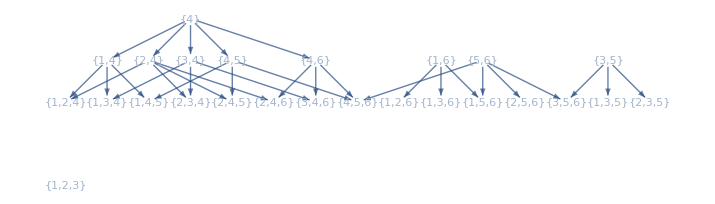

# codimension | 0 | 1 | 2 | 3
# boundaries | 0 | 1 | 8 | 16

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

```mathematica
basis=bdyBasis[[2]]//Flatten
```

{⟨4,7,8⟩,⟨1,4,8⟩,⟨1,6,8⟩,⟨2,4,7⟩,⟨3,4,7⟩,⟨3,5,7⟩,⟨4,5,7⟩,⟨4,6,8⟩,⟨5,6,7⟩,⟨5,6,8⟩,⟨1,2,3⟩,⟨1,2,4⟩,⟨1,2,6⟩,⟨1,3,4⟩,⟨1,3,5⟩,⟨1,3,6⟩,⟨1,4,5⟩,⟨1,5,6⟩,⟨2,3,4⟩,⟨2,3,5⟩,⟨2,4,5⟩,⟨2,4,6⟩,⟨2,5,6⟩,⟨3,4,6⟩,⟨3,5,6⟩,⟨4,5,6⟩}

```mathematica
basis//Length
```

26

```mathematica
EchoTiming[A = AMatrix[]];
A[[1]] // MatrixForm
```

2.12412

((3 e)/(X1+X2+X3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+Y12) | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e/(-X1-X3+Y12+Y23) | 0 | 0 | -(2 e)/(-X1-X3+Y12+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(-X1-X2+Y23) | 0 | 0 | 0 | -(2 e)/(-X1-X2+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 e)/(X1+X2+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2+Y23) | 0 | 0 | 0 | 0 | 0 | (2 e)/(X1+X2+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+X2+Y23)+(2 e)/(X1-X3-Y12+Y23) | -e/(X1+X2+Y23)+e/(X1-X3-Y12+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+X2+Y23) | e/(X1+X2+Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -e/(-X1+Y12+2 Y23) | e/(-X1+Y12+2 Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12+2 Y23) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e/(-X1+Y12) | 0 | 0 | e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12) | 0 | 0 | 0 | 0
0 | 0 | 0 | e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12) | 0 | 0
0 | 0 | 0 | 0 | e/(-X1+Y12) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y12) | 0
0 | 0 | 0 | 0 | 0 | -e/(X1-Y12+2 Y23) | 0 | 0 | -e/(X1-Y12+2 Y23) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1-Y12+2 Y23))

### Basis reduction: filtering

The stored A-matrix from previous overcomplete set of basis functions:

```mathematica
ClearAll[basis,A0,A];
Get[FileNameJoin[{NotebookDirectory[],"storage","basis_three-site"}]];
Get[FileNameJoin[{NotebookDirectory[],"storage","A_three-site"}]];
Get[FileNameJoin[{NotebookDirectory[],"storage","A0_three-site"}]];
```

```mathematica
basis//Length
A0[[1]]//Length
A[[1]]//Length
```

26

26

25

```mathematica
Amatrix=ATotal[A0];
%//MatrixForm
```

(3 e Log[X1+X2+X3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2+X3-Y12]+Log[X1+Y12]) | e (2 Log[X2+X3-Y12]+Log[X1+Y12]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+Y12]+2 Log[X2+X3+Y12]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X3-Y12-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | e (2 Log[X1+X3-Y12-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | e (2 Log[X1+X2-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2+Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X3-Y23]+Log[X1+X2+Y23]) | 0 | 0 | 0 | 0 | 0 | e (Log[X3-Y23]+2 Log[X1+X2+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1-Y12]+Log[X2+X3+Y12]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+2 Log[X2+X3+Y12]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2+Y23]+2 Log[X1-X3-Y12+Y23]) | e (-Log[X1+X2+Y23]+Log[X1-X3-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2+X3+Y12]-Log[X1+X2+Y23]) | e (2 Log[X2+X3+Y12]+Log[X1+X2+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3+Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (-Log[X3-2 Y12-Y23]+Log[X2+Y12+Y23]) | 0 | e (-Log[X1+Y12]+Log[X3-2 Y12-Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3-2 Y12-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X2-Y12-Y23]-Log[X3+Y23]) | 0 | 0 | e (-Log[X1+Y12]+Log[X2-Y12-Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X2-Y12-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y12]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3+Y23]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X2+Y12-Y23]-Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X3-Y23]-Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | e (-Log[X1+Y12]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3-Y23]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X3+2 Y12-Y23]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y12]+Log[X3+2 Y12-Y23]) | e (Log[X3+2 Y12-Y23]-Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3+2 Y12-Y23]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X1-Y12-2 Y23]-Log[X3+Y23]) | e (-Log[X1-Y12-2 Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12-2 Y23]+Log[X3+Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y12]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3+Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X1-Y12]+Log[X3-Y23]) | 0 | 0 | e (-Log[X1-Y12]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X1-Y12]+Log[X3-Y23]) | 0 | 0 | 0 | e (Log[X3-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y12]+Log[X3-Y23]) | e (Log[X3-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1-Y12]+Log[X2+Y12-Y23]) | 0 | 0 | e (-Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X2+Y12-Y23]-Log[X1-Y12+2 Y23]) | 0 | 0 | e (Log[X3+Y23]-Log[X1-Y12+2 Y23]) | e (-Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2+Y12-Y23]+Log[X3+Y23]+Log[X1-Y12+2 Y23]) | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y12]+Log[X2+Y12+Y23]) | e (-Log[X3-Y23]+Log[X2+Y12+Y23]) | e (-Log[X1-Y12]+Log[X3-Y23]) | e (Log[X3-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]))

```mathematica
Amatrix//Letter
%//Length
```

{X1+X2+X3,X1-Y12,X2+X3-Y12,X1+Y12,X2+X3+Y12,X1-Y12-2 Y23,X1+X2-Y23,X3-Y23,X3-2 Y12-Y23,X2-Y12-Y23,X1+X3-Y12-Y23,X2+Y12-Y23,X3+2 Y12-Y23,X1+X2+Y23,X3+Y23,X2-Y12+Y23,X1-X3-Y12+Y23,X2+Y12+Y23,X1-Y12+2 Y23}

19

#### level 0

```mathematica
dRep=Thread[(d/@basis)->Coefficient[Amatrix,e].basis];
```

```mathematica
l0={Log[X1+Y12],Log[X2+Y12+Y23],Log[X3+Y23]};(*old letters*)
```

```mathematica
Basis={psi};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y12],Log[X3-Y23],Log[X2-Y12-Y23],Log[X2+Y12-Y23],Log[X2-Y12+Y23]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
Basis=Join[Basis,lv2];
```

{-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩-⟨4,5,7⟩,-⟨1,2,6⟩-⟨1,4,5⟩-⟨1,4,8⟩+⟨1,6,8⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨4,6,8⟩,-⟨1,3,4⟩-⟨1,4,8⟩-⟨3,4,7⟩,⟨1,3,6⟩+⟨1,6,8⟩+⟨3,4,6⟩+⟨3,4,7⟩-⟨4,6,8⟩,⟨1,3,5⟩-⟨1,4,5⟩+⟨1,4,8⟩+⟨3,5,7⟩-⟨4,5,7⟩}

5

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basis;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten;
Do[If[CheckDependent[lv2Old,i,Basis],,Join[Basis,lv2Old[[i]]]],{i,1,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

6

#### level 2

```mathematica
d2=Basis[[2;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X2+X3-Y12],Log[X2+X3+Y12],Log[X1+X2-Y23],Log[X1+X2+Y23]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
2 ⟨1,4,8⟩-⟨4,7,8⟩ | -2 ⟨1,4,8⟩+⟨4,7,8⟩
2 ⟨3,4,7⟩-⟨4,7,8⟩ | -2 ⟨3,4,7⟩+⟨4,7,8⟩
2 ⟨3,5,7⟩-2 ⟨4,5,7⟩-⟨4,7,8⟩ | -2 ⟨3,5,7⟩+2 ⟨4,5,7⟩+⟨4,7,8⟩
2 ⟨1,6,8⟩-2 ⟨4,6,8⟩-⟨4,7,8⟩ | -2 ⟨1,6,8⟩+2 ⟨4,6,8⟩+⟨4,7,8⟩)

{2 ⟨1,4,8⟩-⟨4,7,8⟩,2 ⟨3,4,7⟩-⟨4,7,8⟩,2 ⟨3,5,7⟩-2 ⟨4,5,7⟩-⟨4,7,8⟩,2 ⟨1,6,8⟩-2 ⟨4,6,8⟩-⟨4,7,8⟩}

```mathematica
Basis=Join[Basis,lv3];
Basis//Length
```

10

```mathematica
Basis//Length
```

10

```mathematica
lv3Old=Coefficient[d2,#]&/@l1//Flatten;
Do[If[CheckDependent[lv3Old,i,Basis],,Basis=Append[Basis,lv3Old[[i]]]],{i,1,Length[lv3Old]}]
Basis//Length
```

13

#### level 3

```mathematica
d3=Basis[[7;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l3=Cases[%,_Log,Infinity]//Union;
Complement[l3,l2]
```

{Log[X1+X2+X3]}

```mathematica
Coefficient[d3,#]&/@Complement[l3,l2];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 11x1 to 3*)
lv4=%[[All;;,1]]
```

{-3 ⟨4,7,8⟩}

```mathematica
Basis=Join[Basis,lv4];
Basis//Length
```

14

```mathematica
lv4Old=Coefficient[d3,#]&/@(Complement[l3,Complement[l3,l2]])//Flatten;
Do[If[CheckDependent[lv4Old,i,Basis],,Basis=Append[Basis,lv4Old[[i]]]],{i,1,Length[lv4Old]}]
Basis//Length
```

16

#### close at level 3:

```mathematica
letters={l0,l1,l2,l3}//Flatten//Union
%//Length
```

{Log[X1+X2+X3],Log[X1-Y12],Log[X2+X3-Y12],Log[X1+Y12],Log[X2+X3+Y12],Log[X1+X2-Y23],Log[X3-Y23],Log[X2-Y12-Y23],Log[X2+Y12-Y23],Log[X1+X2+Y23],Log[X3+Y23],Log[X2-Y12+Y23],Log[X2+Y12+Y23]}

13

```mathematica
d4=Basis/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l4=Cases[%,_Log,Infinity]//Union;
Complement[l4,letters]
```

{}

so there is no new letters appearing.

```mathematica
lv5Old=Coefficient[d3,#]&/@letters//Flatten;
Do[If[CheckDependent[lv5Old,i,Basis],,Basis=Append[Basis,lv5Old[[i]]]],{i,1,Length[lv5Old]}]
Basis//Length
```

16

since there is no new basis introduced, we show that the differentiation closes at level 3.

#### summary: all physical basis

16 = 1 + 5 + (4+3) + (1+2)
13 = 3 + 5 + 4 + 1

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩
-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩-⟨4,5,7⟩
-⟨1,2,6⟩-⟨1,4,5⟩-⟨1,4,8⟩+⟨1,6,8⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨4,6,8⟩
-⟨1,3,4⟩-⟨1,4,8⟩-⟨3,4,7⟩
⟨1,3,6⟩+⟨1,6,8⟩+⟨3,4,6⟩+⟨3,4,7⟩-⟨4,6,8⟩
⟨1,3,5⟩-⟨1,4,5⟩+⟨1,4,8⟩+⟨3,5,7⟩-⟨4,5,7⟩
2 ⟨1,4,8⟩-⟨4,7,8⟩
2 ⟨3,4,7⟩-⟨4,7,8⟩
2 ⟨3,5,7⟩-2 ⟨4,5,7⟩-⟨4,7,8⟩
2 ⟨1,6,8⟩-2 ⟨4,6,8⟩-⟨4,7,8⟩
⟨2,4,5⟩-⟨2,4,6⟩-⟨4,5,7⟩-⟨4,6,8⟩+⟨4,7,8⟩
⟨3,4,6⟩-⟨3,4,7⟩-⟨4,6,8⟩+⟨4,7,8⟩
-⟨1,4,5⟩-⟨1,4,8⟩-⟨4,5,7⟩+⟨4,7,8⟩
-3 ⟨4,7,8⟩
-2 ⟨4,6,8⟩+2 ⟨4,7,8⟩
-⟨1,4,5⟩-⟨1,4,8⟩+⟨4,5,7⟩-⟨4,7,8⟩)

16

see how this 16d subspace is embedded in the previous 26d space:

```mathematica
(*({{{4}, {⟨4,7,8⟩}}, {{1,4}, {⟨1,4,8⟩}}, {{1,6}, {⟨1,6,8⟩}}, {{2,4}, {⟨2,4,7⟩}}, {{3,4}, {⟨3,4,7⟩}}, {{3,5}, {⟨3,5,7⟩}}, {{4,5}, {⟨4,5,7⟩}}, {{4,6}, {⟨4,6,8⟩}}, {{1,2,3}, {⟨1,2,3⟩}}, {{1,2,6}, {⟨1,2,6⟩}}, {{1,3,4}, {⟨1,3,4⟩}}, {{1,3,5}, {⟨1,3,5⟩}}, {{1,3,6}, {⟨1,3,6⟩}}, {{1,4,5}, {⟨1,4,5⟩}}, {{2,3,5}, {⟨2,3,5⟩}}, {{2,4,5}, {⟨2,4,5⟩}}, {{2,4,6}, {⟨2,4,6⟩}}, {{3,4,6}, {⟨3,4,6⟩}}})*)
```

```mathematica
Basis/.Thread[basis->(Subscript[φ,#]&/@Range[basis//Length])]//MatrixForm
```

(φ_11-φ_13-φ_14+φ_15+φ_16-φ_17-φ_20+φ_21-φ_22+φ_24
-φ_5+φ_6-φ_7-φ_20+φ_21-φ_22+φ_24
-φ_2+φ_3-φ_8-φ_13-φ_17+φ_21-φ_22
-φ_2-φ_5-φ_14
φ_3+φ_5-φ_8+φ_16+φ_24
φ_2+φ_6-φ_7+φ_15-φ_17
-φ_1+2 φ_2
-φ_1+2 φ_5
-φ_1+2 φ_6-2 φ_7
-φ_1+2 φ_3-2 φ_8
φ_1-φ_7-φ_8+φ_21-φ_22
φ_1-φ_5-φ_8+φ_24
φ_1-φ_2-φ_7-φ_17
-3 φ_1
2 φ_1-2 φ_8
-φ_1-φ_2+φ_7-φ_17)

### A matrix

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basis[[j]]],{i,1,Length[Basis]},{j,1,Length[basis]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix16=Umatrix.Amatrix.Uinv//Simplify;
%//MatrixForm
```

(e (Log[X1+Y12]+Log[X3+Y23]+Log[X2+Y12+Y23]) | e (Log[X1-Y12]-Log[X1+Y12]) | e (Log[X3-Y23]-Log[X3+Y23]) | e (Log[X2-Y12-Y23]-Log[X2+Y12+Y23]) | e (Log[X2+Y12-Y23]-Log[X2+Y12+Y23]) | e (Log[X2-Y12+Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1-Y12]+Log[X3+Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2-Y23]+Log[X2+Y12-Y23]) | e (Log[X1+X2+Y23]-Log[X2+Y12+Y23]) | 0 | e (Log[X3-Y23]-Log[X3+Y23]) | e (Log[X2+Y12-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | e (-Log[X2+X3-Y12]+Log[X2-Y12+Y23]) | 0 | 0 | e (Log[X2+X3+Y12]-Log[X2+Y12+Y23]) | e (Log[X1-Y12]-Log[X1+Y12]) | 0 | e (Log[X2-Y12+Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0
0 | 0 | 0 | e (Log[X1+Y12]+Log[X2-Y12-Y23]+Log[X3+Y23]) | 0 | 0 | e (-Log[X2+X3-Y12]+Log[X3+Y23]) | e (Log[X1+Y12]-Log[X1+X2-Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0 | e (-Log[X1+Y12]+Log[X1+X2-Y23]) | 0 | e (Log[X2+X3+Y12]-Log[X3+Y23]) | 0 | e (Log[X1-Y12]-Log[X1+Y12]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3+Y23]+Log[X2-Y12+Y23]) | e (Log[X2+X3-Y12]-Log[X3+Y23]) | 0 | e (-Log[X1+Y12]+Log[X1+X2+Y23]) | 0 | 0 | 0 | e (Log[X3-Y23]-Log[X3+Y23]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X2+X3-Y12]+Log[X1+Y12]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2+X3]-Log[X1+Y12]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2+X3]-Log[X3+Y23]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2+Y23]+Log[X3+Y23]) | 0 | 0 | 0 | e (Log[X3-Y23]-Log[X3+Y23]) | e (Log[X1+X2+X3]-Log[X3+Y23]) | 0 | e (-Log[X3-Y23]+Log[X3+Y23])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+2 Log[X2+X3+Y12]) | 0 | 0 | 0 | e (Log[X1+X2+X3]-Log[X1+Y12]) | e (Log[X1-Y12]-Log[X1+Y12]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | e (Log[X1+X2+Y23]-Log[X2+Y12+Y23]) | e (-Log[X1+X2+X3]+Log[X2+X3+Y12]+Log[X1+X2+Y23]-Log[X2+Y12+Y23]) | e (Log[X2+X3+Y12]-Log[X2+Y12+Y23]) | e (-Log[X1+X2+Y23]+Log[X2+Y12+Y23])
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2-Y23]+Log[X2+Y12-Y23]) | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | e (-Log[X1+X2+X3]+Log[X2+X3+Y12]) | e (Log[X2+X3+Y12]-Log[X3+Y23]) | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2+X3-Y12]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | e (Log[X3-Y23]+Log[X1+X2+Y23]+Log[X2-Y12+Y23]) | e (-Log[X1+X2+X3]+Log[X1+X2+Y23]) | 0 | e (Log[X1+Y12]-Log[X1+X2+Y23])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 e Log[X1+X2+X3] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e (-Log[X1+X2+X3]+Log[X2+X3+Y12]) | e (Log[X1-Y12]+2 Log[X2+X3+Y12]) | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2+X3-Y12]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2+Y23]+Log[X2-Y12+Y23]) | e (Log[X1+X2+X3]-Log[X1+X2+Y23]) | 0 | e (Log[X1+Y12]+Log[X3-Y23]+Log[X1+X2+Y23]))

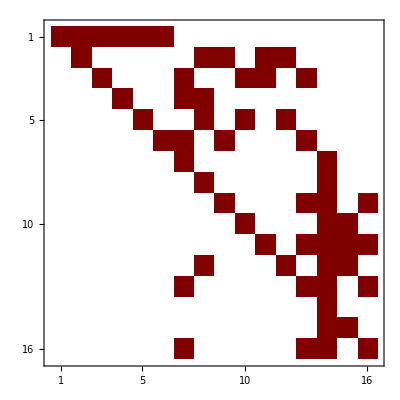

```mathematica
Amatrix16//MatrixPlot
```

the matrix is not upper triangular...
we need to orthogonalize the new basis appearing at each level.

#### check flatness

```mathematica
Coefficient[Amatrix16,e];
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

#### recover A matrix in kinematic flow

```mathematica
basisKinematic={⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩,-⟨2,3,5⟩+⟨2,3,7⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨2,6,7⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩+⟨3,6,7⟩-⟨4,5,7⟩,-⟨1,2,6⟩+⟨1,2,9⟩-⟨1,4,5⟩+⟨1,4,9⟩-⟨1,5,9⟩-⟨1,6,9⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩+⟨4,6,9⟩,⟨1,3,5⟩-⟨1,3,8⟩-⟨1,4,5⟩+⟨1,4,8⟩-⟨3,5,8⟩+⟨4,5,8⟩,-⟨1,3,4⟩+⟨1,3,8⟩-⟨1,4,8⟩+⟨3,4,8⟩,⟨1,3,6⟩-⟨1,3,8⟩+⟨1,6,8⟩+⟨3,4,6⟩-⟨3,4,8⟩-⟨4,6,8⟩,⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩-⟨2,6,7⟩-⟨2,7,9⟩-⟨4,5,7⟩+⟨4,6,9⟩-⟨4,7,9⟩+⟨5,7,9⟩+⟨6,7,9⟩,⟨3,5,7⟩-⟨3,5,8⟩+⟨3,7,8⟩-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩,-⟨3,4,7⟩+⟨3,4,8⟩-⟨3,7,8⟩+⟨4,7,8⟩,⟨3,4,6⟩-⟨3,4,8⟩+⟨3,6,7⟩+⟨3,7,8⟩-⟨4,6,8⟩-⟨6,7,8⟩,-⟨1,4,5⟩+⟨1,4,8⟩-⟨1,5,9⟩+⟨1,8,9⟩+⟨4,5,8⟩-⟨5,8,9⟩,-⟨1,4,8⟩+⟨1,4,9⟩-⟨1,8,9⟩+⟨4,8,9⟩,⟨1,6,8⟩-⟨1,6,9⟩+⟨1,8,9⟩-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩,-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩+⟨5,7,9⟩-⟨5,8,9⟩+⟨7,8,9⟩,⟨4,7,8⟩-⟨4,7,9⟩+⟨4,8,9⟩-⟨7,8,9⟩,-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩-⟨6,7,8⟩+⟨6,7,9⟩+⟨7,8,9⟩};
```

this is troublesome. We should do a composition : 16x26 times 26x16 to obtain this 16x16 U matrix, as we need to use the 26d quotient space.

```mathematica
UmatrixK0=Table[Coefficient[basisKinematic[[i]]/.sol,basis[[j]]],{i,1,Length[basisKinematic]},{j,1,Length[basis]}];
UK0inv=Simplify[PseudoInverse[UmatrixK0]];
```

```mathematica
UmatrixK0//Dimensions
UK0inv//Dimensions
```

{16,26}

{26,16}

```mathematica
UmatrixK=UmatrixK0.Uinv;
UKinv=Simplify[Inverse[UmatrixK]];
```

```mathematica
AmatrixK=UmatrixK.Amatrix16.UKinv//Simplify;
%//MatrixForm
```

(e (Log[X1+Y12]+Log[X3+Y23]+Log[X2+Y12+Y23]) | e (Log[X1-Y12]-Log[X1+Y12]) | e (Log[X3-Y23]-Log[X3+Y23]) | e (Log[X2-Y12+Y23]-Log[X2+Y12+Y23]) | e (Log[X2-Y12-Y23]-Log[X2+Y12+Y23]) | e (Log[X2+Y12-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1-Y12]+Log[X3+Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | e (Log[X3-Y23]-Log[X3+Y23]) | e (Log[X1+X2+Y23]-Log[X2+Y12+Y23]) | e (Log[X1+X2-Y23]-Log[X2+Y12+Y23]) | e (Log[X2+Y12-Y23]-Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | e (Log[X1-Y12]-Log[X1+Y12]) | 0 | 0 | 0 | e (Log[X2-Y12+Y23]-Log[X2+Y12+Y23]) | e (Log[X2+X3-Y12]-Log[X2+Y12+Y23]) | e (Log[X2+X3+Y12]-Log[X2+Y12+Y23]) | 0 | 0 | 0
0 | 0 | 0 | e (Log[X1+Y12]+Log[X3+Y23]+Log[X2-Y12+Y23]) | 0 | 0 | 0 | e (-Log[X1+Y12]+Log[X1+X2+Y23]) | 0 | 0 | e (Log[X3-Y23]-Log[X3+Y23]) | e (-Log[X2+X3-Y12]+Log[X3-Y23]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X2-Y12-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | e (-Log[X1+Y12]+Log[X1+X2-Y23]) | 0 | 0 | e (Log[X2+X3-Y12]-Log[X3+Y23]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0 | e (Log[X1-Y12]-Log[X1+X2-Y23]) | e (Log[X1-Y12]-Log[X1+Y12]) | 0 | 0 | e (Log[X2+X3+Y12]-Log[X3+Y23]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]+Log[X3-Y23]+Log[X2+Y12+Y23]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2+Y23]-Log[X2+Y12+Y23]) | e (Log[X1+X2+X3]-Log[X2+Y12+Y23]) | e (Log[X2+X3+Y12]-Log[X2+Y12+Y23])
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2+Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | e (Log[X3-Y23]-Log[X3+Y23]) | e (-Log[X1+X2+X3]+Log[X3-Y23]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2+X3]-Log[X3+Y23]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y12]-Log[X1+X2-Y23]) | e (Log[X1-Y12]+Log[X2+Y12-Y23]+Log[X3+Y23]) | 0 | 0 | 0 | 0 | 0 | e (Log[X2+X3+Y12]-Log[X3+Y23])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+Log[X3-Y23]+Log[X2-Y12+Y23]) | e (-Log[X2+X3-Y12]+Log[X3-Y23]) | 0 | e (-Log[X1+Y12]+Log[X1+X2+Y23]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X2+X3-Y12]+Log[X1+Y12]) | 0 | 0 | e (Log[X1+X2+X3]-Log[X1+Y12]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y12]+2 Log[X2+X3+Y12]) | 0 | e (-Log[X1+X2+X3]+Log[X1-Y12]) | e (Log[X1-Y12]-Log[X1+Y12])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X3-Y23]+2 Log[X1+X2+Y23]) | e (-Log[X1+X2+X3]+Log[X3-Y23]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 e Log[X1+X2+X3] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2+X3]+Log[X1-Y12]) | e (Log[X1-Y12]+2 Log[X2+X3+Y12]))

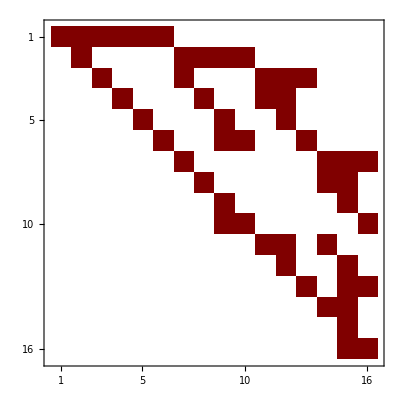

```mathematica
AmatrixK//MatrixPlot
```

### Differential equations

Translate A-matrix to ODE of the correlator: